# Tadpole Image Processing Pipeline

## Updated 10/21/24

## Made by Willem Nielsen for The Tadpole Project. Any issues contact willemnielsen1@gmail.com

## Import

Here we import our image files and then convert them to images. You will have to update the path. You can find the images here (You need drive permissions).

```mathematica
imagePath = "Projects/Wolfram/Tadpoles/1/";
imageFiles=FileNames["*.jpg", imagePath];
imgs=Import/@imageFiles;
```

## Processing

### Neural Net

Here we define a function that takes a neural net and runs an image through it in our case we will be using a Wolfram Net Model.

```mathematica
netevaluate[net_, img_, device_ : "CPU"] := Round@ArrayResample[net[img, TargetDevice -> device], Reverse@ImageDimensions[img], Resampling -> "Bilinear"];
```

Now we use the net model to get the masks. The masks are just the data that the neural net outputs. It contains the locations for which pixels the neural net thinks are part of the object.

```mathematica
masks=netevaluate[NetModel["U2-Net Trained on DUTS-TR Data"],#, "CPU"] & /@ imgs;
```

Now we convert those masks to images. Here I make them small for style reasons, but this can be changed by increasing the “100”.

```mathematica
maskImgs = Image[#, ImageSize->{100, Automatic}]&/@ masks;
idxs = Range[Length@imgs];
```

Here’s what a single mask image looks like:

```mathematica
maskImgs[[1]]
```

-Graphics-

In this folder we have 39 of these images:

```mathematica
Length@maskImgs
```

39

### Getting Coords and Building Graphic

Next we define a function that takes as input the mask image, and gives us a set of coordinates boundaries. The amount of coordinates can be adjusted by n. The more coordinates the more detailed the outline will be. But, this makes it harder for the human to adjust the shape later on.

```mathematica
getBoundCoords[img_, n_ : 20] := Module[{mcs, idxs}, 
  mcs = MeshCoordinates[ImageMesh[img]];
  idxs = Round[Subdivide[1, Length@mcs, n]];
  mcs[[idxs]]
]
```

Get coordinates

```mathematica
bcs = getBoundCoords/@ maskImgs;
```

MeshCoordinates::argx: MeshCoordinates called with 21 arguments; 1 argument is expected.

Now we overlay the polygon on the image. This will allow us to view and edit what the neural net came up with

```mathematica
graphics = MapThread[Graphics[{#1, FaceForm[Transparent], EdgeForm[{Red, Thick}],Polygon[#2]}, ImageSize->Large]&,{imgs, bcs}];
```

Here’s what a single graphic looks like. Notice how you can double click the polygon and change the coordinates.

```mathematica
graphics[[1]]
```

-Graphics-

Here’s an example of the graphic after I changed the coordinates

## Editing Suite

So now that we have these graphic objects, that allow us to view and edit the neural net interpretation, we can use the editing suite to do this as efficiently as possible. Here we will view, edit and save the new coordinates and images as we go. Here we define our functions that we will use.

```mathematica
outputPath = "Projects/Wolfram/Tadpoles/Output10-21";
```

Here we define our functions and parameters for the editing suite.

```mathematica
outputGraphics = graphics;
outputCoords = getCoords/@ graphics;
currentIdx = 0;
```

```mathematica
openNext[idx_ : -1, graphics_ : graphics] := Module[{}, 
  If[idx == -1,
   currentIdx = currentIdx + 1,
   currentIdx = idx,
   ] ;
graphics[[currentIdx]]
  ]
  
getCoords[graphic_] := Module[{shape}, 
  shape = First@Cases[graphic[[1]], _Polygon | _BezierCurveBox, Infinity (*This searches through all nested levels*)];
  shape[[1]]
  ]

save[graphic_, overwrite_:True] := Module[{}, 
  outputGraphics[[currentIdx]] = graphic;
  outputCoords[[currentIdx]] = getCoords@graphic;
  Export[FileNameJoin[{outputPath, "image" <> ToString[currentIdx] <> ".png"}], graphic, OverwriteTarget -> overwrite];
  Export[FileNameJoin[{outputPath, "coords" <> ToString[currentIdx] <> ".csv"}], outputCoords[[currentIdx]], OverwriteTarget -> overwrite];
  ]
  
saveAllGraphics[graphics_List, overwrite_:False] := MapIndexed[Export[FileNameJoin[{outputPath, "image" <> ToString[First[#2]] <> ".png"}], #1, OverwriteTarget->overwrite] &, graphics]

saveAllCoords[coords_List, overwrite_:False] := MapIndexed[Export[FileNameJoin[{outputPath, "coords" <> ToString[First[#2]] <> ".csv"}], Prepend[#, {"x", "y"}], OverwriteTarget->overwrite] &, coords]
```

Here is the suite. Simply run openNext and you get the graphics output. Double click the image, and then double click the polygon to edit it. Drag the white points until satisfied. Select the image and press (⌘C). Then, put your cursor in between the  brackets of the save functions, press ⌘V and the image will be pasted into the function. Run the cell to save the new graphic and coordinates. It will save these to the outputPath specified at the top of the editing suite section.

```mathematica
currentIdx
```

0

```mathematica
openNext[]
```

The overwrite option is set to True by default, but you can change this by entering False as the second argument in save, or edit the inside of the function.

```mathematica
save[-Graphics-]
```

You can also choose to save all graphics at the end here. The overwrite option is set to False by default so you don’t accidentally erase all your outputs.

```mathematica
saveAllGraphics[outputGraphics]
saveAllCoords[outputCoords]
```

### View Previous Output

```mathematica
updatedimgs = Import["Projects/Wolfram/Tadpoles/Output10-21/image2.png"]
```

-Graphics-

```mathematica
ucoords = Rest@Import["Projects/Wolfram/Tadpoles/Output10-21/coords2.csv"]
```

{{201.194,671.877},{225.454,571.929},{312.731,519.376},{413.231,458.376},{632.731,442.399},{705.716,441.255},{945.633,432.079},{1097.73,448.326},{1224.82,502.094},{1386.86,571.044},{1410.78,617.599},{1360.53,706.628},{1166.53,715.546},{1014.59,732.358},{867.444,731.16},{714.798,730.984},{616.783,745.123},{516.445,742.21},{407.75,784.565},{258.718,740.488},{204.165,682.872}}

```mathematica
outputCoords[[2]]
```

{{210.964,680.501},{235.224,580.553},{322.5,528.},{423.,467.},{642.501,451.023},{715.485,449.879},{955.403,440.703},{1107.5,456.95},{1234.59,510.718},{1396.63,579.668},{1420.55,626.224},{1312.5,634.},{1118.51,642.918},{1023.5,650.03},{864.,664.5},{719.5,681.982},{621.485,696.121},{502.499,712.972},{402.532,758.176},{268.487,749.112},{213.934,691.496}}

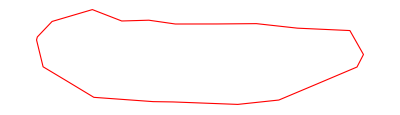

```mathematica
Graphics[{EdgeForm[Red], FaceForm[White], Polygon[ucoords]}]
```